# MMA 进行 PPT 演示

## 一个演示样例 Date 2023-03-31

## Section 1 基本功能

### Subsection 1.1 公式

SideNotes 单元

SideNotes 和 SideCode 单元不会显示在演讲中.

Clear["Global`"]
<< MaTeX`

MaTeX[{"\frac{x^2}{\sqrt{3}}",
HoldForm[Integrate[Sin[x],{x,0,2 Pi}]],Expand[(1+x)^5]}
]

{,,}

(* 可以直接使用 MaTeX 插入数学公式 *)
MaTeX["\sum_{k=1}^{\infty} \frac{1}{k^2} = \frac{\pi^2}{6}"]
MaTeX["\alpha + \beta = \gamma"]

-Graphics-

LATEX 公式输入是支持的

Plot[Sin[x], {x, -2*Pi, 2*Pi}]

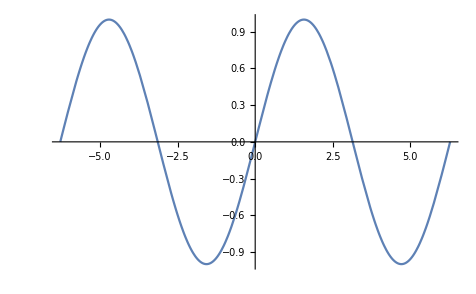

引理:  这个就是著名的欧拉公式

```mathematica
MaTeX[{"\\frac{x^2}{\\sqrt{3}}",
	HoldForm[Integrate[Sin[x],{x,0,2 Pi}]],Expand[(1+x)^5]}
]
```

MaTeX[{\frac{x^2}{\sqrt{3}},∫_0^(2 π) Sin[x]ⅆx,1+5 x+10 x^2+10 x^3+5 x^4+x^5}]

MaTeX 支持实时渲染

### Subsection 1.2 图片插入

下面就是一张简单的图片

-Graphics-

## Section 2 MMA的强项

### Subsection 2.1 动态演示

Manipulate[Plot[Sin[a x+b],{x,0,6}],{{a,2,"周期T"},1,4},{{b,0,"初识相位"},0,10}]

VectorPlot3D[{x, y, z}, {x, -1, 1}, {y, -1, 1}, {z,-1, 1},PlotTheme→"Classic"]

-Graphics3D-

g=RandomGraph[{20,100}];
h=FindHamiltonianCycle[g];
Legended[HighlightGraph[g,Style[h,Directive[Thick,Red]]],LineLegend[{Directive[Thick,Red]},{"Hamiltonian cycle"}]]

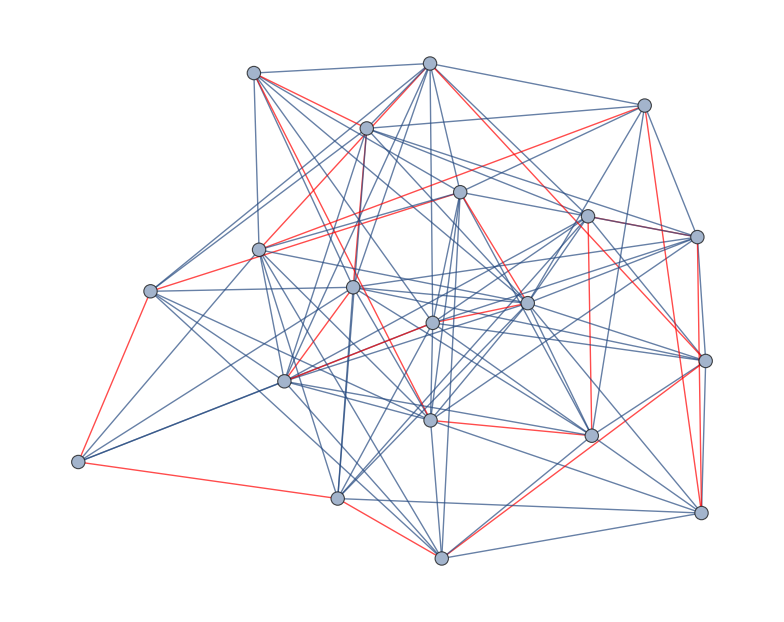

Manipulate[
Plot[n x (1-x^2)^n,{x, -5, 5},
	PlotRange→{-10, 10},
	PlotStyle→{Red},
	AxesLabel→{x, y},
	AxesStyle→Arrowheads[{0,0.03}]
],
{n, 1, 50}]

Set::write: Inherited[State] 中的标签 Inherited 被保护.

Show[DiscretePlot[1/n,{n,1,100, 2}],DiscretePlot[2/n,{n,0,100, 2}]]

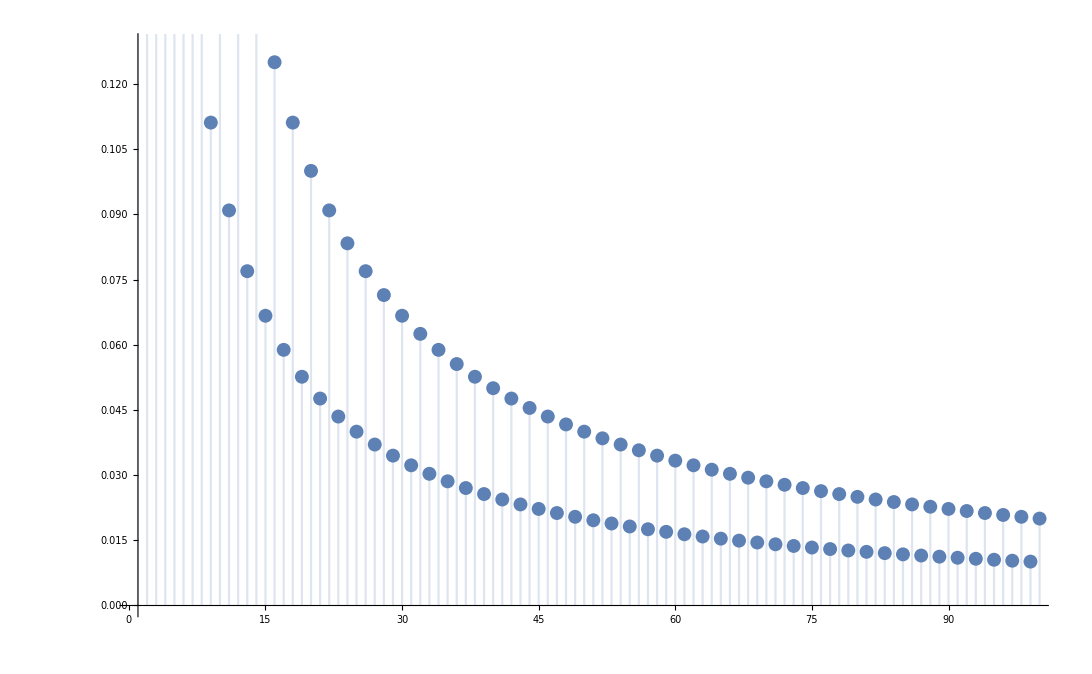

## Last Section

Thank You